```mathematica
Clear["Global`*"];
Remove["Global`*"];
SetDirectory[NotebookDirectory[]];
```

## Import Files

```mathematica
readMatlabComplex[file_]:=ToExpression[StringSplit[StringReplace[ReadList[file,"String"],{"e"->"*10^","i"->"*I"}],","]]
```

```mathematica
allFiles=FileNames["*.csv"];
allData=readMatlabComplex[#]&/@allFiles;
```

ToExpression::sntx: Invalid syntax in or before "sampl*Ing rat*10^: 78.125 MHz".
                                                                   ^

ToExpression::sntx: Invalid syntax in or before "*Int*10^grator crossov*10^r 174.6 kHz".
                                                  ^

ToExpression::sntx: Invalid syntax in or before "*Int*10^grator saturat*Ion +43.0 dB".
                                                  ^

General::stop: Further output of ToExpression::sntx
     will be suppressed during this calculation.

ToExpression::sntxi: Incomplete expression; more input is needed .

General::stop: Further output of ToExpression::sntxi
     will be suppressed during this calculation.

```mathematica
numoffiles=Dimensions[allFiles][[1]];
index=Table[i,{i,1,numoffiles}];
fileswithindex=Thread[{index,allFiles}];
dataset=Table[allData[[i]][[19;;]],{i,1,numoffiles}];
numset=Table[Dimensions[dataset[[i]]][[1]],{i,1,numoffiles}];
fileswithindex
```

{{1,100100P_20230417_201152_HighResData.csv},{2,100100X_20230417_201126_HighResData.csv},{3,LPam0pm_10_20230412_214245_HighResData.csv},{4,LPam_10pm0_20230412_213845_HighResData.csv},{5,Lpamoffpmoff_20230412_212225_HighResData.csv},{6,LXam0pm_10_20230412_214340_HighResData.csv},{7,LXam_10pm0_20230412_213812_HighResData.csv},{8,LXamoffpmoff_20230412_212345_HighResData.csv},{9,offoffP2_20230417_201024_HighResData.csv},{10,offoffX2_20230417_201057_HighResData.csv}}

## Density matrix in Fock basis

```mathematica
bin=160; (*Dimension of Discretized quadrature value Better be even?*)
n=8;  (*Photon number cutoff*)
dim=n+1; (*Dimension of density matrix*)

(*Ensuring positive semidefiniteness, trace property*)
rr=LowerTriangularize[Array[Subscript[r,##]&,{dim,dim}]];
ii=LowerTriangularize[Array[Subscript[im,##]&,{dim,dim}]];
ii=ii-DiagonalMatrix[Diagonal[ii]];
ii=ⅈ*ii;
t=rr+ii;
(*Density Matrix*)
ρ= ConjugateTranspose[t] . t/Tr[ConjugateTranspose[t] . t] ;
```

## Fock State Wave Function

```mathematica
fn=16;(*Pre-caculation*) 
psi[m_,x_]=HermiteH[m,x]/(√(2^m m!√π))Exp[-x^2/2]; (*wave functions in the Fock basis*)
Tpsi=Table[psi[m,x],{m,0,fn}];
```

## Shot Noise Unit Estimation

```mathematica
size1=Dimensions[allData[[9]][[19;;]]];
size1=size1[[1]];
vacp=Table[allData[[9]][[19;;]][[i]][[2]],{i,1,size1}];
snu1=StandardDeviation[vacp]
mp=Mean[vacp]

size2=Dimensions[allData[[10]][[19;;]]];
size2=size2[[1]];
vacx=Table[allData[[10]][[19;;]][[i]][[2]],{i,1,size2}];
snu2=StandardDeviation[vacx]
mx=Mean[vacx]
(*Shot noise unit is manually fit to match vacuum data with our theoretical expectation*)
snu=(snu1+snu2)/1.5;
```

4.86853×10^-6

-0.0000116228

4.88555×10^-6

-0.0000116536

## Discretizing Phase Space of the Signal

```mathematica
slice=snu*n/(bin/2);
xevent=ConstantArray[0,bin+1];
pevent=ConstantArray[0,bin+1];

(*X-Quadrature of the Data*)
x1size=Dimensions[allData[[6]][[19;;]]];
x1size=x1size[[1]]
x1quad=Table[allData[[6]][[19;;]][[i]][[2]],{i,1,x1size}];

(*P-Quadrature of the Data*)
p1size=Dimensions[allData[[3]][[19;;]]];
p1size=p1size[[1]]
p1quad=Table[allData[[3]][[19;;]][[i]][[2]],{i,1,p1size}];

(*X-Quadrature of the Data*)
x2size=Dimensions[allData[[7]][[19;;]]];
x2size=x2size[[1]]
x2quad=Table[allData[[4]][[19;;]][[i]][[2]],{i,1,x2size}];

(*P-Quadrature of the Data*)
p2size=Dimensions[allData[[4]][[19;;]]];
p2size=p2size[[1]]
p2quad=Table[allData[[4]][[19;;]][[i]][[2]],{i,1,p2size}];

xsize=x1size+x2size
psize=p1size+p2size
xquad=Join[x1quad,x2quad];
pquad=Join[p1quad,p2quad];
```

16377

16377

16377

«1 more identical outputs»

32754

32754

## Counting Events

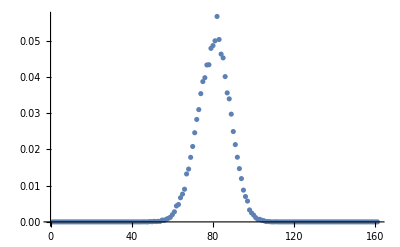

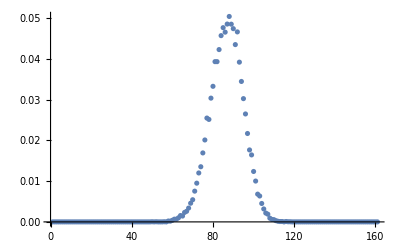

```mathematica
(*Counting Occurence*)
For[i=1,i<xsize+1,i++,
xevent[[Round[(xquad[[i]]-mx)/slice]+bin/2]]=xevent[[Round[(xquad[[i]]-mx)/slice]+bin/2]]+1;]

For[i=1,i<psize+1,i++,
pevent[[Round[(pquad[[i]]-mp)/slice]+bin/2]]=pevent[[Round[(pquad[[i]]-mp)/slice]+bin/2]]+1;]

(*Normalization*)
xevent=xevent/xsize;
pevent=pevent/psize;

(*Gmn is imported, discretized and normalized occurence of event*)
G={xevent,pevent}//N;
ListPlot[xevent, PlotRange->Full]
ListPlot[pevent,PlotRange->Full]
```

## Normalization Parameter for Projector

10.

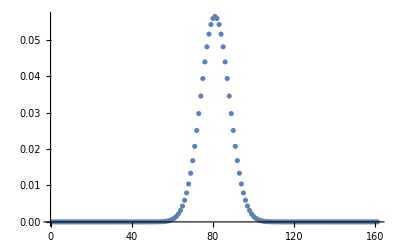

10.

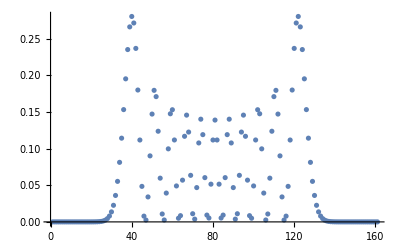

0.0135784

0.0145093

```mathematica
hermite0=Table[(psi[0,(i-bin/2)/(bin/2)*n])^2,{i,0,bin}];
norm=Sum[hermite0[[i]],{i,1,bin+1}];
norm//N
hermite0=hermite0/norm;
ListPlot[hermite0,PlotRange->Full]
hermite1=Table[(psi[10,(i-bin/2)/(bin/2)*n])^2,{i,0,bin}];
norm1=Sum[hermite1[[i]],{i,1,bin+1}];
norm1//N
ListPlot[hermite1,PlotRange->Full]
(*Just to see the similarity real quick*)
StandardDeviation[xevent]//N
StandardDeviation[hermite0]//N
```

## Projector Represented in quadrature basis

```mathematica
(*Matrix Element in Fock basis*)
Π=Table[(Tpsi[[a+1]]Tpsi[[b+1]]/norm)ⅇ^(ⅈ(b-a)θ),{a,0,n},{b,0,n}] ;
```

## Discretize X and θ

```mathematica
theta={0,Pi/2};
quad=Subdivide[-n,n,bin];
```

## Deviation Function

```mathematica
(*note that we do not use mean photon number because phase averaged measurement is not available*)
Q=Re[
Sum[(      G[[j,i]]-(  Tr[Π.ρ]/.{x->quad[[i]],θ->theta[[j]]}  )   )^2,{i,1,bin+1},{j,1,2}]
];
```

## Optimization Kernel

```mathematica
flat1=DeleteCases[Flatten[rr],_Integer];
flat2=DeleteCases[Flatten[-ⅈ*ii],_Integer];
kernel=Join[flat1,flat2];
```

## Maximum Entropy reconstruction

```mathematica
solution=FindMinimum[Q,kernel];

Chop[ρ /. solution[[2]] ];

Chop[MatrixForm[ρ /. solution[[2]]]]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

(0.760627 | -0.0084557+0.290218 ⅈ | -0.0818673-0.021822 ⅈ | 0.00120876-0.036513 ⅈ | -0.00860587-0.000979316 ⅈ | 0.00544653-0.0121619 ⅈ | -0.00406893-0.00862998 ⅈ | -0.0112514+0.00155189 ⅈ | 0.0102718+0.00481348 ⅈ
-0.0084557-0.290218 ⅈ | 0.190269 | -0.01569+0.054703 ⅈ | -0.0184177+0.0018748 ⅈ | -0.000405311+0.00811177 ⅈ | -0.00875955+0.00063013 ⅈ | -0.00281633+0.00370934 ⅈ | 0.0028744+0.0061959 ⅈ | 0.000142949-0.00512988 ⅈ
-0.0818673+0.021822 ⅈ | -0.01569-0.054703 ⅈ | 0.0216215 | 0.00054692+0.00992666 ⅈ | -0.0011299-0.0038835 ⅈ | 0.000707597+0.000489091 ⅈ | 0.0000650257+0.00188458 ⅈ | 0.0028027-0.0023917 ⅈ | -0.00236254-0.00163892 ⅈ
0.00120876+0.036513 ⅈ | -0.0184177-0.0018748 ⅈ | 0.00054692-0.00992666 ⅈ | 0.0112568 | -0.00472013+0.0050368 ⅈ | -0.00154119+0.000656018 ⅈ | 0.0030486+0.000951417 ⅈ | -0.00208492-0.00259309 ⅈ | -0.00327742+0.00293698 ⅈ
-0.00860587+0.000979316 ⅈ | -0.000405311-0.00811177 ⅈ | -0.0011299+0.0038835 ⅈ | -0.00472013-0.0050368 ⅈ | 0.00874722 | 0.00226901+0.00244166 ⅈ | -0.000142896-0.00271452 ⅈ | -0.000132666+0.00219906 ⅈ | 0.00335545+0.00111473 ⅈ
0.00544653+0.0121619 ⅈ | -0.00875955-0.00063013 ⅈ | 0.000707597-0.000489091 ⅈ | -0.00154119-0.000656018 ⅈ | 0.00226901-0.00244166 ⅈ | 0.00234987 | -0.000524137-0.00114127 ⅈ | 0.000249186-0.000125596 ⅈ | 0.0012265-0.0000648381 ⅈ
-0.00406893+0.00862998 ⅈ | -0.00281633-0.00370934 ⅈ | 0.0000650257-0.00188458 ⅈ | 0.0030486-0.000951417 ⅈ | -0.000142896+0.00271452 ⅈ | -0.000524137+0.00114127 ⅈ | 0.00132016 | -0.000590948-0.000503696 ⅈ | -0.000813089+0.00140869 ⅈ
-0.0112514-0.00155189 ⅈ | 0.0028744-0.0061959 ⅈ | 0.0028027+0.0023917 ⅈ | -0.00208492+0.00259309 ⅈ | -0.000132666-0.00219906 ⅈ | 0.000249186+0.000125596 ⅈ | -0.000590948+0.000503696 ⅈ | 0.00163453 | -0.000246987-0.00118833 ⅈ
0.0102718-0.00481348 ⅈ | 0.000142949+0.00512988 ⅈ | -0.00236254+0.00163892 ⅈ | -0.00327742-0.00293698 ⅈ | 0.00335545-0.00111473 ⅈ | 0.0012265+0.0000648381 ⅈ | -0.000813089-0.00140869 ⅈ | -0.000246987+0.00118833 ⅈ | 0.00217358)

## Plotting Real part of Density Matrix

```mathematica
DiscretePlot3D[Abs@Re[ρ /. solution[[2]]][[i+1, j+1]], {i, 0, n}, {j, 0, n}, 
 ExtentSize -> Full]
```

-Graphics3D-

## Plotting Imaginary part

```mathematica
DiscretePlot3D[Abs@Im[ρ /. solution[[2]]][[i+1, j+1]], {i, 0, n}, {j, 0, n}, 
 ExtentSize -> Full]
```

-Graphics3D-

## Wigner Reconstruction

```mathematica
g=2;
M=4;
xrange={-5,5};
yrange={-5,5};
linespace=100;
rho=ρ /. solution[[2]];
%//MatrixForm;
meshgrid[x_List,y_List]:={ConstantArray[x,Length[x]],Transpose@ConstantArray[y,Length[y]]}
{xx,yy}=meshgrid[Array[#&,linespace,xrange],Array[#&,linespace,yrange]];
aa=0.5*g*(xx+ⅈ yy);
%//MatrixForm;
wlist=Table[Table[Table[0,{i,1,M}],{j,1,M}],{k,1,M}];
wlist[[1]]=Exp[-2 Abs[aa]^2]/π;
W=Re[rho[[1,1]]]*Re[wlist[[1]]];

For[nn=1, nn<M,nn++,
wlist[[nn+1]]=(2.0*aa*wlist[[nn]])/√nn;
W+=2*Re[rho[[1,nn+1]]*wlist[[nn+1]]];
]


For[mm=1, mm<M,mm++,

temp=wlist[[mm+1]];
wlist[[mm+1]]=(2*Conjugate[aa]*temp-√mm*wlist[[mm]])/√mm;
W+=Re[rho[[mm+1,mm+1]]*wlist[[mm+1]]];
For[nn=mm+1, nn<M,nn++,
temp2=(2*aa*wlist[[nn]]-√mm*temp)/√nn;
temp=wlist[[nn+1]];
wlist[[nn+1]]=temp2;
W+=2*Re[rho[[mm+1,nn+1]]*wlist[[nn+1]]];
]
]
(*Plotting Wigner function. Grid not properly drawn yet*)
ListPlot3D[0.5*W*g^2,PlotRange->All, Boxed->False]
(*Displacement parameter*)
list=0.5*W*g^2;
pos=Position[list,_?(#==Max[list]&)]
disp=Sqrt[((50-pos[[1,1]])/10)^2+((50-pos[[1,2]])/10)^2]//N
```

-Graphics3D-

{{46,50}}

0.4